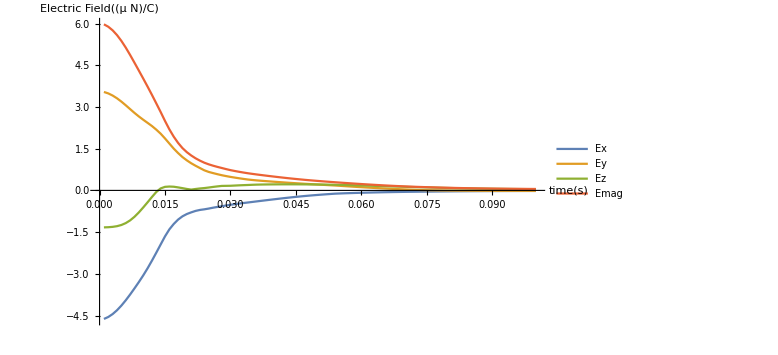

-Graphics3D-

```mathematica
(*
Written by K.Roos
Department of Mechanical Engineering
Bradley University

NOTE:This implementation of the Charges in a Spherical Conductor
(originally produced by Larry Engelhardt in python) contains the basic
structure for calculating the dynamical motion of charges that interact
via the Coulomb interation, using a typical Molecular Dynamics pair
potential approach. It does not attempt to animate the motion of the
charges during the calculation (although there are several ways to accomplish this in Mathematica),but only plots the final position of the
charges (including an image of the spherical conductor)
in a 3D scatter plot after the program has looped through the
specified number of time steps.
*)

ClearAll["Global`*"]

(*set physical parameter values*)
ncharges=100; (*number of individual charges*)
Q=5.0×10^-6; (*net excess charge in Coulombs*)
m=1.0×10^-3; (*mass of each charge in kg*) 
R=0.1; (*radius of conducting sphere in meters*) 
k=8.99×10^9; (*Coulomb constant*) 
qi=Q/ncharges; (*charge on each individual charge*)

(* Coordinates of field point P -- Electric field components due
 to all the charges will be calculated at this point*)
Px=-0.05;
Py=0.043;
Pz=-0.01;

(*algorithmic parameters*)
Δt=0.001; (*time step in seconds*)
tsteps=100; (*total number of time steps*)

(*Create charges with random initial positions (all initially at rest). The center of the spherical conductor of radius R is at the origin.*)
For[i=1,i≤ncharges,i++,
x[i]=(-1)^IntegerPart[2*RandomReal[]]*R/Sqrt[3]*RandomReal[];
y[i]=(-1)^IntegerPart[2*RandomReal[]]*R/Sqrt[3]*RandomReal[];
z[i]=(-1)^IntegerPart[2*RandomReal[]]*R/Sqrt[3]*RandomReal[];
vx[i]=0;
vy[i]=0;
vz[i]=0;
]
(*Initialize electric field components for each time step to zero*)
For[n=1,n≤tsteps,n++,
Ex[n]=0;
Ey[n]=0;
Ez[n]=0;
]

(*Main loop*)
For[n=1,n≤tsteps,n++,
time[n]=n*Δt;
(* reset net force in x,y,z directions to zero for all charges *)
   For[i=1,i≤ncharges,i++,
fx[i]=0;
fy[i]=0;
fz[i]=0;
]
(*Calculate forces on each pair of charges by considering
i-j pairs. The structure of the nested for loops prevents double counting of
    pairs.*)
For[i=1,i≤ncharges-1,i++,
For[j=i+1,j≤ncharges,j++,
dx=x[i]-x[j];
	dy=y[i]-y[j];
	dz=z[i]-z[j];
	rmag=Sqrt[dx*dx+dy*dy+dz*dz];
(*Magnitude of mutual Coulomb force between charges i and j*)
	fij=k*qi*qi/(rmag*rmag);
(*The three spatial components of the force between charges
i and j*)	
fijx=fij*dx/rmag;
	fijy=fij*dy/rmag;
	fijz=fij*dz/rmag;
(*Accumulation of the componenets of the net force acting on
      charges i and j*)
	fx[i]+=fijx;
	fy[i]+=fijy;
	fz[i]+=fijz;
	fx[j]+=-fijx;
	fy[j]+=-fijy;
	fz[j]+=-fijz;
]
]
(* velocities and positions updated for all charges *)
For[i=1,i≤ncharges,i++,
(* rescale acceleration in case of huge value encountered *)
  xaccel[i]=fx[i]/m;
	yaccel[i]=fy[i]/m;
         zaccel[i]=fz[i]/m;
         maga=Sqrt[xaccel[i]*xaccel[i]+yaccel[i]*yaccel[i]+zaccel[i]*zaccel[i]];
     If[maga>1000,
xaccel[i]=1000*xaccel[i]/maga;
yaccel[i]=1000*yaccel[i]/maga;
zaccel[i]=1000*zaccel[i]/maga;
];
(* Euler-Cromer algorithm for updataing velocities and positions *)
  vx[i]+=xaccel[i]*Δt;
	vy[i]+=yaccel[i]*Δt;
	vz[i]+=zaccel[i]*Δt;
       x[i]+=vx[i]*Δt; 
	     y[i]+=vy[i]*Δt;
	     z[i]+=vz[i]*Δt;
	(* d is the distance from center of sphere to charge*)
  d=Sqrt[x[i]*x[i]+y[i]*y[i]+z[i]*z[i]];
 (*if charge moved beyond surface of conuctor,bring it back to surface*)
   If[d>R,
x[i]=x[i]*R/d;
y[i]=y[i]*R/d;
z[i]=z[i]*R/d;
 ];
(* Calculation of Electric Field components at point P*)
dxP=Px-x[i];
       dyP=Py-y[i];
       dzP=Pz-z[i];
       rvector=Sqrt[dxP^2+dyP^2+dzP^2];
      (* Each E-field component, as well as the magnitude of the
    electric field vector is calculated. Units of micro-N/C for
    the electric field are used for ease in plotting.*)
Ex[n]=Ex[n]+10^-6*k*qi/rvector^2*(dxP/rvector);
       Ey[n]=Ey[n]+10^-6*k*qi/rvector^2*(dyP/rvector);
       Ez[n]=Ez[n]+10^-6*k*qi/rvector^2*(dzP/rvector);
       Emag[n]=Sqrt[Ex[n]^2+Ey[n]^2+Ez[n]^2];
]
] (* end of main loop *)
(*Plotting commands*)
tx=Table[{time[i],Ex[i]},{i,1,tsteps}];
ty=Table[{time[i],Ey[i]},{i,1,tsteps}];
tz=Table[{time[i],Ez[i]},{i,1,tsteps}];
tmag=Table[{time[i],Emag[i]},{i,1,tsteps}];
ListLinePlot[{tx,ty,tz,tmag},ImageSize-> Large,PlotRange->All,AxesLabel->{HoldForm[time[s]],HoldForm[Electric Field [μ N/C]]},PlotLabel->None,PlotLegends->{"Ex","Ey","Ez","Emag"},LabelStyle->{FontFamily->"Arial",18,GrayLevel[0]}]
plot=Table[{x[i],y[i],z[i]},{i,1,ncharges}];
Graphics3D[{Opacity[0.5],Sphere[{0,0,0},R],Blue,PointSize[0.015],Point[plot],PlotMarkers->{"Sphere",Medium},Axes->True,BoxRatios->1},ImageSize->Large,PlotRange->{{-R,R},{-R,R},{-R,R}},Lighting->Automatic]
```